# Solving 3 equations(R, d, y)

```mathematica
Clear[r]
d[t_]:=Sqrt[r^2+R[t]^2-2*r(r*Cos[ϕ[t]]^2-Sin[ϕ[t]]*Sqrt[R[t]^2-r^2*Cos[ϕ[t]]^2])];
FullSimplify[D[d[t],t]]
```

((√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]]) (R[t] R'[t]+r Cos[ϕ[t]] (√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]]) ϕ'[t]))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))

```mathematica
Clear[r,k]
Eb[t_]:=k*π*(1-Sqrt[1-(r*Cos[ϕ[t]]/R[t])^2]);
FullSimplify[D[Eb[t], t]]
```

-(k π r^2 Cos[ϕ[t]] (Cos[ϕ[t]] R'[t]+R[t] Sin[ϕ[t]] ϕ'[t]))/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

```mathematica
V[t_]:=π/(12*d[t])*(R[t]-d[t]+r)^2*(d[t]^2+2*d[t]*r-3*r^2+2*d[t]*R[t]+6*r*R[t]-3*R[t]^2);
FullSimplify[D[V[t], t]]
```

(π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) d'[t]+4 d[t] R[t] R'[t]))/(4 d[t]^2)

```mathematica
expr=(1/(4 d[t]^2))π (r+d[t]-R[t]) (r-d[t]+R[t]) ((r-d[t]-R[t]) (r+d[t]+R[t]) Derivative[1][d][t]+4 d[t] R[t] Derivative[1][R][t]);
sol=Solve[expr==α,Derivative[1][d][t]];
FullSimplify[sol]
```

{{d'[t]→(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) R'[t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]))}}

```mathematica
expr1=((Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]+r Sin[ϕ[t]]) (R[t] Derivative[1][R][t]+r Cos[ϕ[t]] (Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2]+r Sin[ϕ[t]]) Derivative[1][ϕ][t]))/(Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sqrt[R[t]^2+r (-r Cos[2 ϕ[t]]+2 Sqrt[-r^2 Cos[ϕ[t]]^2+R[t]^2] Sin[ϕ[t]])]);
expr2=(4 d[t] (α d[t]+π R[t] (-r-d[t]+R[t]) (r-d[t]+R[t]) Derivative[1][R][t]))/(π (r-d[t]-R[t]) (r+d[t]-R[t]) (r-d[t]+R[t]) (r+d[t]+R[t]));


collected=FullSimplify[expr1-expr2];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Dcoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Ecoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Fterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Dcoeff*Derivative[1][R][t]+Ecoeff*Derivative[1][ϕ][t]==Fterm;
```

R[t] (-((4 d[t])/((-r+d[t]+R[t]) (r+d[t]+R[t])))+(√(-r^2 Cos[ϕ[t]]^2+R[t]^2)+r Sin[ϕ[t]])/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2) √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]]))))

(r Cos[ϕ[t]] √(R[t]^2+r (-r Cos[2 ϕ[t]]+2 √(-r^2 Cos[ϕ[t]]^2+R[t]^2) Sin[ϕ[t]])))/(√(-r^2 Cos[ϕ[t]]^2+R[t]^2))

(4 α d[t]^2)/(π (d[t]^4+(r^2-R[t]^2)^2-2 d[t]^2 (r^2+R[t]^2)))

```mathematica
EL[t_]:=2*π*r*Γ Cos[ϕ[t]];
FullSimplify[D[EL[t], t]]
```

-2 π r Γ Sin[ϕ[t]] ϕ'[t]

```mathematica
Clear[k,r,σ,X,z,y,w,v,Np,Γ, P]
expr3=-((k*Pi*r^2*Cos[ϕ[t]]*
    (Cos[ϕ[t]]*Derivative[1][R][
       t] + R[t]*Sin[ϕ[t]]*
      Derivative[1][ϕ][t]))/
   (Sqrt[1 - (r^2*Cos[ϕ[t]]^2)/
       R[t]^2]*R[t]^3));
expr4=4 π σ r^2Cos[ϕ[t]]*Derivative[1][ϕ][t];
expr5=2*π*r*(-Γ)*Sin[ϕ[t]]*Derivative[1][ϕ][t];
expr6=α*P;
expr7=(G/π)*z^2*w*v*Cos[ϕ[t]]*Np/y;
expr8=X;
lhs=expr7+expr8;
rhs=expr3+expr4+expr5+expr6;

collected=FullSimplify[lhs-rhs];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Acoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Bcoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Cterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Acoeff*Derivative[1][R][t]+Bcoeff*Derivative[1][ϕ][t]==Cterm
```

(k π r^2 Cos[ϕ[t]]^2)/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

π r (2 Γ Sin[ϕ[t]]+r Cos[ϕ[t]] (-4 σ+(k Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)))

-X+P α-(G Np v w z^2 Cos[ϕ[t]])/(π y)

(k π r^2 Cos[ϕ[t]]^2 R'[t])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)+π r (2 Γ Sin[ϕ[t]]+r Cos[ϕ[t]] (-4 σ+(k Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2))) ϕ'[t]==-X+P α-(G Np v w z^2 Cos[ϕ[t]])/(π y)

# Using Bending

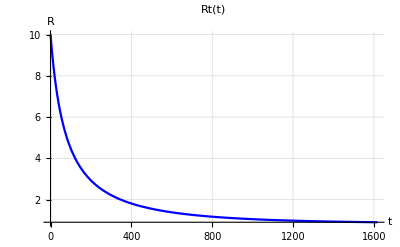

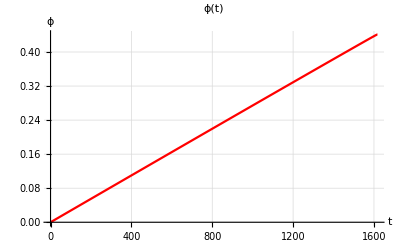

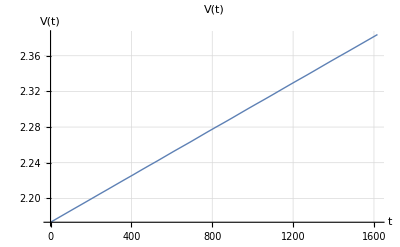

Variable | 1617 Value at t =
RtFinal | 0.904325+0. ⅈ
phiFinal | 0.441+0. ⅈ
dtFinal | 0.426864+0. ⅈ
A1Final | 154702.+0. ⅈ
B1Final | 18125.3+0. ⅈ
C1Final | -0.785807+0. ⅈ
D1Final | 44529.9+0. ⅈ
E1Final | 19009.1+0. ⅈ
F1Final | -0.0000506803+0. ⅈ
RdotFinal | -7.00054×10^-6+0. ⅈ
phdotFinal | 0.0000163965+0. ⅈ
EbdotFinal | 0.00027621+0. ⅈ
EbFinal | 3.14152+0. ⅈ
EsdotFinal | 0.595551+0. ⅈ
EsFinal | 8221.28+0. ⅈ

/home/soumyadeep/Desktop/Sporulation/Codes_N/InitialData.dat

```mathematica
ClearAll["Global`*"]

(*Constants*)

(*w=30*10^-9;
z=3.4*10^-9;
y=2*10^-9;
σ=4.5*10^-3;*)
r=1;
(*v=15*10^-9;
k=11250*10^-21;
α=0.058*10^-18/3600;*)
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
(*Np=2;*)

Gt=1;(*Value of G*)
Xt=0.0;(*External Energy*)
Γt=0;(*value of Line tension*)
σt=800; (*value of surface term*)
Rt0=10;
ph0=0.;
tmin=0;
tmax=2000;
tminp=0;
finalTime=1617;
(*Define d,A-F as functions of R[t],ph[t]*)

dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[ϕ[t]]^2-Sin[ϕ[t]]*Sqrt[Rt[t]^2-Cos[ϕ[t]]^2])];

A1[t_]:=(π Cos[ϕ[t]]^2)/(Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^3);


B1[t_]:=(2 Γt Sin[ϕ[t]]+Cos[ϕ[t]] (-4 σt+(Sin[ϕ[t]])/(Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2]Rt[t]^2)));

C1[t_]:=(-Xt+P αt-Gt Cos[ϕ[t]]);

D1[t_]:=Rt[t] (-((4 dt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2]+Sin[ϕ[t]])/(Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sqrt[(Rt[t]^2+(- Cos[2 ϕ[t]]+2 Sqrt[(-Cos[ϕ[t]]^2+Rt[t]^2)] Sin[ϕ[t]]))]));

E1[t_]:=(Cos[ϕ[t]] Sqrt[Rt[t]^2+ (- Cos[2 ϕ[t]]+2 Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])])/Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] ;

F1[t_]:=(4 αp dt[t]^2)/(π 2 (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)));
(*Checking*)
(*params={Rt[t]->4,ϕ[t]->0.3};
Evaluate/@{dt[t], A1[t],B1[t], C1[t], D1[t], E1[t], F1[t]}/.params*)
(****************)

(*RHS of system*)
Rdot[t_]:=(E1[t]*C1[t]-B1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);
phdot[t_]:=(-D1[t]*C1[t]+A1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);

(*Define ODEs*)
eqns={Rt'[t]==Rdot[t],ϕ'[t]==phdot[t],Rt[0]==Rt0,ϕ[0]==ph0};

(*Numerical solution*)sol=NDSolve[eqns,{Rt,ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];

V[t_]:=π/(12*dt[t])*(Rt[t]-dt[t]+1)^2*(dt[t]^2+2*dt[t]*1-3+2*dt[t]*Rt[t]+6*Rt[t]-3*Rt[t]^2)

(*Plot R vs t*)
rPlot=Plot[Evaluate[Rt[t]/.sol],{t,tminp,tmax},PlotLabel->"Rt(t)",AxesLabel->{"t","R"},PlotStyle->Blue,PlotRange->All,GridLines->Automatic]

(*Plot φ vs t*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

test1Plot=Plot[Evaluate[Rt[t]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2",AxesLabel->{"t","R^2)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
test2Plot=Plot[Evaluate[Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->" Cos^2(ϕ(t))",AxesLabel->{"t"," Cos^2(ϕ"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
testPlot=Plot[Evaluate[Rt[t]^2-Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2 - Cos^2(ϕ(t))",AxesLabel->{"t","R^2-Cos^2(ϕ)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
dtPlot=Plot[Evaluate[dt[t]/.sol],{t,tminp, tmax},PlotLabel->"d(t)",AxesLabel->{"t","d(t)"},PlotStyle->{Thick,Purple},GridLines->Automatic,PlotRange->All];
testVPlot=Plot[Evaluate[V[t]/.sol],{t,0,tmax},PlotLabel->" V(t)",AxesLabel->{"t"," V(t)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
(*Display both plots*)
GraphicsGrid[{{rPlot},{phPlot}, {testPlot}, {test1Plot}, {test2Plot}, {dtPlot}}];
(*term check*)
Eb[t_]:=π*(1-Sqrt[1-(Cos[ϕ[t]]/Rt[t])^2]);
Ebdot[t_]:=-((Pi*Cos[ϕ[t]]*    (Cos[ϕ[t]]*Rdot[t] + Rt[t]*Sin[ϕ[t]]*phdot[t]))/   (Sqrt[1 - (Cos[ϕ[t]]^2)/Rt[t]^2]*Rt[t]^3));
Es[t_]:=4*π*σt*Rt[t]^2*(1-Sqrt[1-(Cos[ϕ[t]]/Rt[t])^2]);
Esdot[t_]:=(1/(Sqrt[1 - (Cos[ϕ[t]]^2)/Rt[t]^2]*Rt[t]))*(4*Pi*σt*((Cos[ϕ[t]]^2 + 2*(-1 + Sqrt[1 -  (Cos[ϕ[t]]^2)/ Rt[t]^2])*Rt[t]^2)* Rdot[t] -   Cos[ϕ[t]]*Rt[t]*Sin[ϕ[t]]* phdot[t]));
RtFinal=Rt[finalTime]/.sol//First//N;
phiFinal=ϕ[finalTime]/.sol//First//N;
dtFinal=dt[finalTime]/.sol//First//N;
A1Final=A1[finalTime]/.sol//First//N;
B1Final=B1[finalTime]/.sol//First//N;
C1Final=C1[finalTime]/.sol//First//N;
D1Final=D1[finalTime]/.sol//First//N;
E1Final=E1[finalTime]/.sol//First//N;
F1Final=F1[finalTime]/.sol//First//N;
RdotFinal=Rdot[finalTime]/.sol//First//N;
phdotFinal=phdot[finalTime]/.sol//First//N;
EbdotFinal=Ebdot[finalTime]/.sol//First//N;
EsdotFinal=Esdot[finalTime]/.sol//First//N;
EbFinal=Eb[finalTime]/.sol//First//N;
EsFinal=Es[finalTime]/.sol//First//N;

TextGrid[{{"Variable",finalTime"Value at t =" },{"RtFinal",RtFinal},{"phiFinal",phiFinal},{"dtFinal",dtFinal},{"A1Final",A1Final},{"B1Final",B1Final},{"C1Final",C1Final},{"D1Final",D1Final},{"E1Final",E1Final},{"F1Final",F1Final},{"RdotFinal",RdotFinal},{"phdotFinal",phdotFinal},{"EbdotFinal",EbdotFinal},{"EbFinal",EbFinal},{"EsdotFinal",EsdotFinal},{"EsFinal",EsFinal}},Frame->All,Background->{None,{{LightGray,None}}}]
tValues=Range[tminp,finalTime,0.1];(*adjust step as needed*)(*Step 2:Build table with shifted time and real parts*)data=Table[{N[t],N[Re[First[Rt[t]/.sol]]],N[Re[First[ϕ[t]/.sol]]], N[Re[First[V[t]/.sol]]]},{t,tValues}];;




(*Step 4:Define full path to Desktop CSV file*)
outputPath=FileNameJoin[{$HomeDirectory,"Desktop","Sporulation","Codes_N","InitialData.dat"}];

(*Step 5:Export as CSV*)
Export[outputPath,data,"Table"]
```

```mathematica
Clear[k,r,σ,X,z,y,w,v,Np,Γ, P]
expr3=(k π r^2 Cos[ϕ[t]] (Cos[ϕ[t]] Derivative[1][R][t]+R[t] Sin[ϕ[t]] Derivative[1][ϕ][t]))/(Sqrt[1-(r^2 Cos[ϕ[t]]^2)/R[t]^2] R[t]^3);
expr4=4 π σ r^2Cos[ϕ[t]]*Derivative[1][ϕ][t];
expr5=2*π*r*(-Γ)*Sin[ϕ[t]]*Derivative[1][ϕ][t];
expr6=α*P;
expr7=(G/π)*z^2*w*v*Cos[ϕ[t]]*Np/y;
expr8=X;
lhs=expr7+expr8;
rhs=expr3+expr4+expr5+expr6;

collected=FullSimplify[lhs-rhs];

(*Step 2:Collect derivative terms*)
collectedExpr=Collect[collected,{Derivative[1][R][t],Derivative[1][ϕ][t]},Simplify];

(*Step 3:Extract coefficients cleanly*)
Acoeff=Coefficient[collectedExpr,Derivative[1][R][t]]//FullSimplify
Bcoeff=Coefficient[collectedExpr,Derivative[1][ϕ][t]]//FullSimplify

(*Step 4:Extract non-derivative part cleanly*)
Cterm=-collectedExpr/.{Derivative[1][R][t]->0,Derivative[1][ϕ][t]->0}//FullSimplify

(*Step 5:Final equation*)
finalEqn=Acoeff*Derivative[1][R][t]+Bcoeff*Derivative[1][ϕ][t]==Cterm;
```

-(k π r^2 Cos[ϕ[t]]^2)/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^3)

π r (2 Γ Sin[ϕ[t]]+r Cos[ϕ[t]] (-4 σ-(k Sin[ϕ[t]])/(√(1-(r^2 Cos[ϕ[t]]^2)/R[t]^2) R[t]^2)))

-X+P α-(G Np v w z^2 Cos[ϕ[t]])/(π y)

# With Bending Final

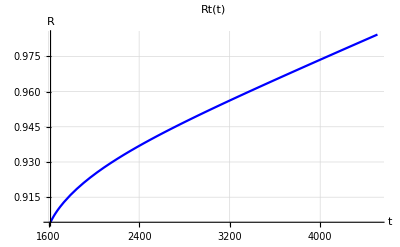

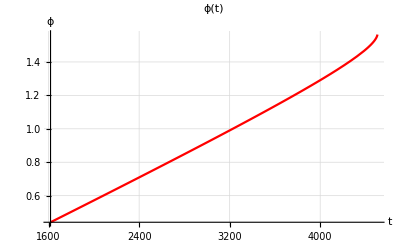

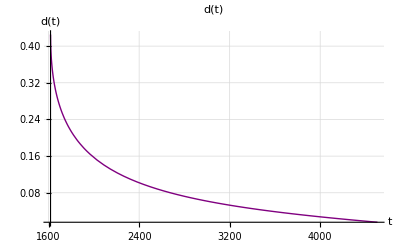

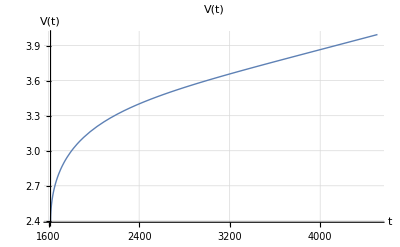

Variable | Value at t = InitialTime
RtInitial | 0.904325
phiInitial | 0.441004
dtInitial | 0.425236
A1Initial | -1949.41
B1Initial | -3158.7
C1Initial | -0.985805
D1Initial | -1.09925
E1Initial | 0.384551
F1Initial | -1.63349×10^-7
RdotInitial | 0.0000899154
phdotInitial | 0.0002566
EbdotInitial | 0.3888
EbInitial | 3.14719
EsdotInitial | 1019.12
EsInitial | 8236.11

/home/soumyadeep/Desktop/Sporulation/Codes_N/shiftedRealData.dat

```mathematica
ClearAll["Global`*"]

(*Constants*)

(*w=30*10^-9;
z=3.4*10^-9;
y=2*10^-9;
σ=4.5*10^-3;*)
r=1;
(*v=15*10^-9;
k=11250*10^-21;
α=0.058*10^-18/3600;*)
αt=(1/60)/11250;
αp=(1/(60*64));
P=80*10^3;
(*Np=2;*)

Gt=1;(*Value of G*)
Xt=0.2;(*External Energy*)
Γt=0;(*value of Line tension*)
σt=800; (*value of surface term*)
Rt0=0.904325;
ph0=0.441004;

tmin=1617;
tmax=4506;
tminp=tmin;
finalTime=tmax;
InitialTime=tmin;
(*Define d,A-F as functions of R[t],ph[t]*)
dt[t_]:=Sqrt[1+Rt[t]^2-2*(Cos[ϕ[t]]^2+Sin[ϕ[t]]*Sqrt[Rt[t]^2-Cos[ϕ[t]]^2])];

A1[t_]:=-((π Cos[ϕ[t]]^2)/(Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^3));

B1[t_]:=(2 Γt Sin[ϕ[t]]+ Cos[ϕ[t]] (-4 σt-(Sin[ϕ[t]])/(Sqrt[1-(Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^2)));

C1[t_]:=-Xt+P αt-Gt Cos[ϕ[t]];

D1[t_]:=-((4 dt[t] Rt[t])/((-1+dt[t]+Rt[t]) (1+dt[t]+Rt[t])))+(Rt[t] (-Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2]+Sin[ϕ[t]]))/(Sqrt[Rt[t]^2-r (Cos[2 ϕ[t]]+2 Sqrt[-Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])])

E1[t_]:=( Cos[ϕ[t]] Sqrt[Rt[t]^2- ( Cos[2 ϕ[t]]+2 Sqrt[- Cos[ϕ[t]]^2+Rt[t]^2] Sin[ϕ[t]])]);

F1[t_]:=(4 αp dt[t]^2)/(π (dt[t]^4+(1-Rt[t]^2)^2-2 dt[t]^2 (1+Rt[t]^2)))Sqrt[- Cos[ϕ[t]]^2+Rt[t]^2];

(*Checking*)
(*params={Rt[t]->4,ϕ[t]->0.3};
Evaluate/@{dt[t], A1[t],B1[t], C1[t], D1[t], E1[t], F1[t]}/.params*)
(****************)

(*RHS of system*)
Rdot[t_]:=(E1[t]*C1[t]-B1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t]);
phdot[t_]:=(-D1[t]*C1[t]+A1[t]*F1[t])/(A1[t]*E1[t]-B1[t]*D1[t])

(*Define ODEs*)
eqns={Rt'[t]==Rdot[t],ϕ'[t]==phdot[t],Rt[InitialTime]==Rt0,ϕ[InitialTime]==ph0};

(*Numerical solution*)sol=NDSolve[eqns,{Rt,ϕ},{t,tmin,tmax},Method->{"StiffnessSwitching"}, MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10];
V[t_]:=π/(12*dt[t])*(Rt[t]-dt[t]+1)^2*(dt[t]^2+2*dt[t]*1-3+2*dt[t]*Rt[t]+6*Rt[t]-3*Rt[t]^2);

(*Plot R vs t*)
rPlot=Plot[Evaluate[Rt[t]/.sol],{t,tminp,tmax},PlotLabel->"Rt(t)",AxesLabel->{"t","R"},PlotStyle->Blue,PlotRange->All,GridLines->Automatic]

(*Plot φ vs t*)
phPlot=Plot[Evaluate[ϕ[t]/.sol],{t,tminp,tmax},PlotLabel->"ϕ(t)",AxesLabel->{"t","ϕ"},PlotStyle->Red,PlotRange->All,GridLines->Automatic]

test1Plot=Plot[Evaluate[Rt[t]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2",AxesLabel->{"t","R^2)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
test2Plot=Plot[Evaluate[Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->" Cos^2(ϕ(t))",AxesLabel->{"t"," Cos^2(ϕ"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
testPlot=Plot[Evaluate[Rt[t]^2-Cos[ϕ[t]]^2/.sol],{t,tminp,tmax},PlotLabel->"R(t)^2 - Cos^2(ϕ(t))",AxesLabel->{"t","R^2-Cos^2(ϕ)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All];
dtPlot=Plot[Evaluate[dt[t]/.sol],{t,tminp, tmax},PlotLabel->"d(t)",AxesLabel->{"t","d(t)"},PlotStyle->{Thick,Purple},GridLines->Automatic,PlotRange->All]
testVPlot=Plot[Evaluate[V[t]/.sol],{t,tminp,tmax},PlotLabel->" V(t)",AxesLabel->{"t"," V(t)"},PlotStyle->Thick,GridLines->Automatic,PlotRange->All]
(*Display both plots*)
GraphicsGrid[{{rPlot},{phPlot}, {testPlot}, {test1Plot}, {test2Plot}, {dtPlot}}];

(*test terms*)
Eb[t_]:=π*(1+Sqrt[1-(Cos[ϕ[t]]/Rt[t])^2]);
Ebdot[t_]:=( π  Cos[ϕ[t]] (Cos[ϕ[t]] Rdot[t]+Rt[t] Sin[ϕ[t]] phdot[t]))/(Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]^3);
Es[t_]:=4*π*σt*Rt[t]^2*(1+Sqrt[1-(Cos[ϕ[t]]/Rt[t])^2]);
Esdot[t_]:=(4 π σt ((- Cos[ϕ[t]]^2+2 (1+Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2]) Rt[t]^2) *Rdot[t]+ Cos[ϕ[t]] Rt[t] Sin[ϕ[t]] phdot[t]))/(Sqrt[1-( Cos[ϕ[t]]^2)/Rt[t]^2] Rt[t]);

RtInitial=Rt[InitialTime]/.sol//First//N;
phiInitial=ϕ[InitialTime]/.sol//First//N;
dtInitial=dt[InitialTime]/.sol//First//N;
A1Initial=A1[InitialTime]/.sol//First//N;
B1Initial=B1[InitialTime]/.sol//First//N;
C1Initial=C1[InitialTime]/.sol//First//N;
D1Initial=D1[InitialTime]/.sol//First//N;
E1Initial=E1[InitialTime]/.sol//First//N;
F1Initial=F1[InitialTime]/.sol//First//N;
RdotInitial=Rdot[InitialTime]/.sol//First//N;
phdotInitial=phdot[InitialTime]/.sol//First//N;
EbdotInitial=Ebdot[InitialTime]/.sol//First//N;
EsdotInitial=Esdot[InitialTime]/.sol//First//N;
EbInitial=Eb[InitialTime]/.sol//First//N;
EsInitial=Es[InitialTime]/.sol//First//N;

TextGrid[{{"Variable","Value at t = InitialTime"},{"RtInitial",RtInitial},{"phiInitial",phiInitial},{"dtInitial",dtInitial},{"A1Initial",A1Initial},{"B1Initial",B1Initial},{"C1Initial",C1Initial},{"D1Initial",D1Initial},{"E1Initial",E1Initial},{"F1Initial",F1Initial},{"RdotInitial",RdotInitial},{"phdotInitial",phdotInitial},{"EbdotInitial",EbdotInitial},{"EbInitial",EbInitial},{"EsdotInitial",EsdotInitial},{"EsInitial",EsInitial}},Frame->All,Background->{None,{{LightGray,None}}}]
(*Step 1:Define time range*)
tValues=Range[tminp,tmax,0.1];(*adjust step as needed*)(*Step 2:Build table with shifted time and real parts*)data=Table[{N[t],N[Re[First[Rt[t]/.sol]]],N[Re[First[ϕ[t]/.sol]]], N[Re[First[V[t]/.sol]]]},{t,tValues}];;




(*Step 4:Define full path to Desktop CSV file*)
outputPath=FileNameJoin[{$HomeDirectory,"Desktop","Sporulation","Codes_N","shiftedRealData.dat"}];

(*Step 5:Export as CSV*)
Export[outputPath,data,"Table"]
```